```mathematica
$MinPrecision=53;
```

### Defining The Domains

#### u Domain(s)

```mathematica
prec=64;
```

```mathematica
uOuterMin=1/10;
uOuterMax= 11/10;
uOuterDomains=1;
uOuterNodes=80;
uInnerNodes=24;
InterfaceNodes=Table[uOuterMin+i(uOuterMax-uOuterMin)/uOuterDomains,{i,0,uOuterDomains,1}];
```

```mathematica
InterfaceNodes//N
```

{0.1,1.1}

```mathematica
GetuDomain[uOutMin_,uOutmax_,uOutDomains_,uOutNodes_,uInnNodes_,IntfaceNodes_]:=Module[{uu=uOutMin},
XInn=Table[-Cos[Pi i/(uInnNodes-1)],{i,0,uInnNodes-1}];
uInner=N[Table[(IntfaceNodes[[1]]+0)/2+(IntfaceNodes[[1]]-0)/2 XInn[[i]],{i,1,uInnNodes}],prec];
XOut=Table[-Cos[Pi i/(uOutNodes-1)],{i,0,uOutNodes-1}];
uOut=N[Flatten[Table[Table[1/2(IntfaceNodes[[j]]+IntfaceNodes[[j-1]])+1/2(IntfaceNodes[[j]]-IntfaceNodes[[j-1]])XOut[[i]],{i,2,uOutNodes}],{j,2,IntfaceNodes//Length}],1],prec];
Join[uInner,uOut]
]
```

```mathematica
uValues=GetuDomain[uOuterMin,uOuterMax,uOuterDomains,uOuterNodes,uInnerNodes,InterfaceNodes];
```

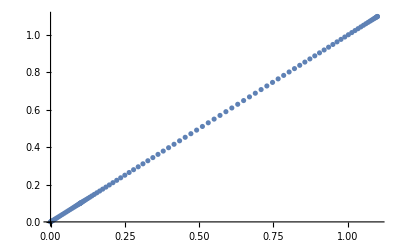

```mathematica
ListPlot[Transpose[{uValues,uValues}]]
```

#### x Domain

```mathematica
xMin=-5;
xMax=5;
xNodes=32;
Deltax=Abs[xMin-xMax]/xNodes;
xValues=Table[xMin+i Deltax,{i,0,xNodes-1}];
```

```mathematica
xValues
```

{-5,-75/16,-35/8,-65/16,-15/4,-55/16,-25/8,-45/16,-5/2,-35/16,-15/8,-25/16,-5/4,-15/16,-5/8,-5/16,0,5/16,5/8,15/16,5/4,25/16,15/8,35/16,5/2,45/16,25/8,55/16,15/4,65/16,35/8,75/16}

#### y Domain

```mathematica
yMin=-5;
yMax=5;
yNodes=32;
Deltay=Abs[yMin-yMax]/yNodes;
yValues=Table[yMin+i Deltay,{i,0,yNodes-1}];
```

```mathematica
yValues
```

{-5,-75/16,-35/8,-65/16,-15/4,-55/16,-25/8,-45/16,-5/2,-35/16,-15/8,-25/16,-5/4,-15/16,-5/8,-5/16,0,5/16,5/8,15/16,5/4,25/16,15/8,35/16,5/2,45/16,25/8,55/16,15/4,65/16,35/8,75/16}

#### Grid

```mathematica
MyGrid=Table[{uValues[[u]],xValues[[x]],yValues[[y]]},{u,1,uValues//Length},{x,1,xValues//Length},{y,1,yValues//Length}];
```

```mathematica
MyGrid//Dimensions
```

{103,32,32,3}

## Boosted Black Brain

## Inhomogeneous boosting

```mathematica
(*gdd=1/ρ^2 Table[ηdd[[u,v]]+,{u,1,4},{v,1,4}]*)
```

#### ρ

```mathematica
modesTot=4;
```

```mathematica
RandomCoefficients=Table[(Random[])/5,{i,1,modesTot}]
```

{0.0756032,0.171627,0.0310439,0.0561683}

```mathematica
RandomCoefficients2=Table[2Pi(Random[]),{i,1,modesTot}]
```

{5.13986,5.96264,2.96584,2.14972}

```mathematica
RandomDirections=Table[{Cos[RandomCoefficients2[[i]]],Sin[RandomCoefficients2[[i]]]}(*{Random[],Random[]}*)//Normalize,{i,1,modesTot}]
```

{{0.414571,-0.910017},{0.949065,-0.315081},{-0.984596,0.174846},{-0.547127,0.83705}}

```mathematica
RandomDirections2=Table[{Cos[RandomCoefficients2[[i]]],Sin[RandomCoefficients2[[i]]]}(*{Random[],Random[]}*)//Normalize,{i,1,modesTot}]
```

{{-0.922499,-0.386},{0.556972,-0.830531},{0.937769,-0.347259},{0.946647,0.322273}}

```mathematica
Norm[RandomCoefficients]
```

0.268553

```mathematica
RandomFactor[{x_,y_}]=(Sum[RandomCoefficients[[i]]Cos[(( i+1) 2Pi x/(xMax-xMin)-(xMax-xMin)/(2Pi( i+1))(RandomReal[]-0.5))]Sin[(( i+1)2Pi y/(xMax-xMin)-(yMax-yMin)/(2Pi( i+1))(RandomReal[]-0.5))],{i,1,modesTot}]);
```

```mathematica
RandomFactor2[{x_,y_}]=0(Sum[RandomCoefficients2[[i]]Cos[(2i Pi (({x,y}.RandomDirections2[[i]])/(xMax-xMin))-(xMax-xMin)(RandomReal[]-0.5))](*+Random[]Sin[(i Pi (y-10(RandomReal[]-0.5)))/(xMax-xMin)]Cos[(i Pi (x-10(RandomReal[]-0.5)))/(yMax-yMin)]*),{i,3,4}(*,{j,7,8}*)](*+Sum[1/100(+Random[]Sin[(i Pi y)/(yMax-yMin)+1.34]),{i,9,10}]*)(*+Sum[1/100(+Random[]Sin[(i Pi x)/(xMax-xMin)+0.23]),{i,9,10}(*,{j,7,8}*)]+Sum[1/100(+Random[]Cos[(i Pi y)/(yMax-yMin)]),{i,9,10}]*))
```

0

#### Proper random function

```mathematica
δuxToInt[x_,y_]:=Table[{{x,y},(Random[]-0.5)/20(*Cos[qx y]+RandomFactor[x,y]*)},{x,xMin,xMax,0.1},{y,yMin,yMax,0.1}];
```

```mathematica
Intδux=Interpolation[δuxToInt[x,y]//Flatten[#,1]&]
```

InterpolatingFunction[…]

```mathematica
XYGrid=Flatten[MyGrid[[1,;;,;;,2;;]],1];
RFTable1=RandomFactor(*[{x,y}]*)/@XYGrid;
(*XYGrid//Dimensions
RFTable//Dimensions*)
```

```mathematica
DataToInt=Table[{{XYGrid[[i,1]],XYGrid[[i,2]]},RFTable1[[i]]},{i,1,RFTable1//Length}];
```

```mathematica
Borders=Join[Select[DataToInt,#[[1,1]]==-5 &],Select[DataToInt,#[[1,2]]==-5 &]]/.-5->5;
BordersData=Join[Table[{{Borders[[n,1,1]],Borders[[n,1,2]]},Borders[[n,2]]},{n,1,Borders//Length}],{{{5,-5},DataToInt[[1,2]]},{{-5,5},DataToInt[[1,2]]}}];
```

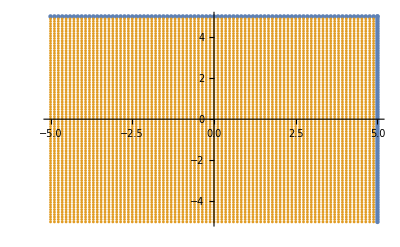

```mathematica
ListPlot[{BordersData[[;;,1]],DataToInt[[;;,1]](*,{{-5,5},{5,-5}}*)},PlotStyle->{PointSize[0.008],PointSize[0.005]}]
```

```mathematica
RFT=Interpolation[Join[DataToInt,BordersData[[2;;]]],Method->"Spline"]
```

InterpolatingFunction[…]

#### Boosting

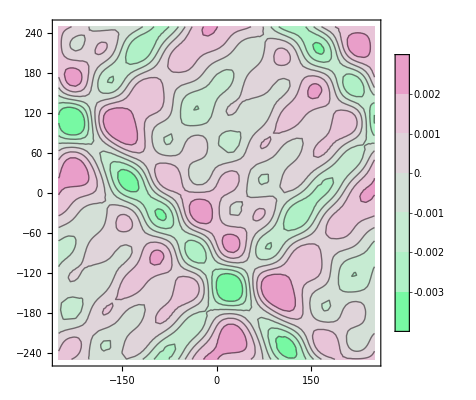

```mathematica
ContourPlot[1/100 RandomFactor[{x,y}],{x,xMin,xMax},{y,yMin,yMax},PlotRange->All,PlotLegends->Automatic,ColorFunction->"MintColors",MaxRecursion->3(*,PlotPoints->20*)]
```

```mathematica
ClearAll[u1d,u0d,u2d]
qx=(4Pi)/(xMax-xMin);
qy=Pi/(yMax-yMin);
(*u0d[x_,y_]=-2^(1/2);*)

u1d[x_,y_]:=(*0.1*)0Cos[qx y] (*+(*RFT[x,y]*)1/100RandomFactor[{x,y}]*);
u2d[x_,y_]:=0(*RandomFactor2[{x,y}]*);
b=1-0.5013868846238644/20^2;
```

The horizon (b) has to be shifted by the energy computed in the masterscalar notebook. also, the 20 squared factor comes from the normalization factor used some paragraphs down.

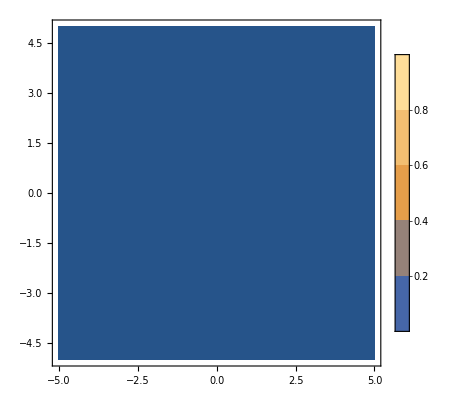

```mathematica
ContourPlot[u1d[x,y],{x,xMin,xMax},{y,yMin,yMax},PlotRange->All,PlotLegends->Automatic(*,ColorFunction->"TemperatureMap"*)(*,MaxRecursion->4*)(*,PlotPoints->20*)]
```

```mathematica
u0d[x_,y_]:=(*u2d[x,y]/.*)Solve[u1d[x,y]^2+u2d[x,y]^2-uu0d[x,y]^2==-1,uu0d[x,y]][[1,1,2]]
```

```mathematica
(*uofρ=NDSolve[{D[u[ρ],ρ]==(u[ρ]^2/ρ^2(1+(b ρ)^3(u1^2+u2^2))^(-1/2)),u[ϵ]==ϵ},u,{ρ,ϵ,1}][[1,1]];*)
```

```mathematica
(*ρofu=DSolve[{D[ρ[u,x,y],{u,1}]==(u^2/ρ[u,x,y]^2(1+(b ρ[u,x,y])^3(u1[x,y]^2+u2[x,y]^2))^(-1/2))^-1},ρ,{u,x,y}][[1,1]];*)
```

Here I compute r in function of rho. I set no boundary conditions for the ODE but I then impose the constant of integration to be zero

```mathematica
rofρ=DSolve[{D[r[ρ,x,y],{ρ}]==(-1/ρ^2(1+(b ρ)^3(u1d[x,y]^2+u2d[x,y]^2))^(-1/2))(*,r[1]==1*)},r,{ρ,x,y}][[1,1]];
rofρ=r/.rofρ//N
```

Function[{ρ,x,y},1./ρ+C[1][x,y]]

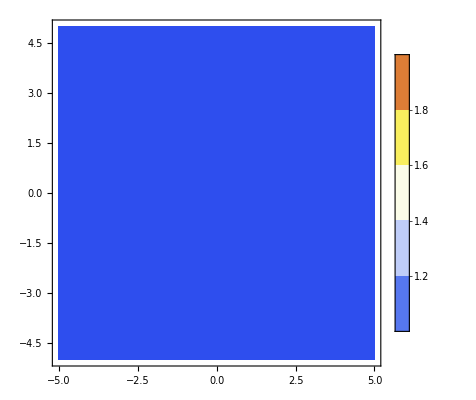

```mathematica
ContourPlot[rofρ[1,x,y]/.C[1][x,y]->0,{x,xMin,xMax},{y,yMin,yMax},PlotRange->All,PlotLegends->Automatic,ColorFunction->"TemperatureMap",MaxRecursion->5(*,PlotPoints->20*)]
```

#### a3

Here I compute the initial data for a3. In the limit at infinity, ρ goes to zero, as u. Anyway, they don’t have the same asymptotic behaviour so we need to take the expansion of A, substitute u to its expression that depends on  ρ, and expand in terms of ρ around infinity (where ρ=0). In this way we have an expression of our variable in terms of ρ at infinity that has to match the expression for A in the Turbulence draft (Eq. 3.7).

```mathematica
AExp=1/u^2+u^2 a3[t,u,x,y]+(2 ξ[t,x,y])/u+ξ[t,x,y]^2-2 Derivative[1,0,0][ξ][t,x,y];
```

```mathematica
AExpOfρ=AExp/.u->rofρ[ρ,x,y]^-1(*/.ξ->Function[{t,z,y},0]*)//Series[#,{ρ,0,2}]&
```

1/ρ^2+(2. ξ[t,x,y]+2. C[1][x,y])/ρ+(ξ[t,x,y]^2+2 ξ[t,x,y] C[1][x,y]+(C[1][x,y])^2-2 ξ^(1,0,0)[t,x,y])+1. a3[t,0,x,y] ρ^2+O[ρ]^3

```mathematica
(*AExpOfρ//Normal//Simplify*)
```

```mathematica
AToMatch=ρ^-2(1-(b ρ)^4(1+u1d[x,y]^2+u2d[x,y]^2))//Simplify
```

1/ρ^2-0.994996 ρ^2

```mathematica
(*AExpOfρ//Normal//Simplify*)
```

Let' s look for ξ

```mathematica
c1Rule=Solve[Coefficient[AExpOfρ,1/ρ]==Coefficient[AToMatch,1/ρ],  C[1][x,y]]//Flatten
```

{C[1][x,y]→-1. ξ[t,x,y]}

Does this work with order term (it has to be checked for every configuration)???

```mathematica
(*SeriesCoefficient[AExpOfρ,{ρ,0,0}]/.c1Rule*)
```

xi can’t depend on t

```mathematica
Coefficient[AToMatch,ρ^2]
```

-0.994996

```mathematica
Coefficient[AExpOfρ,ρ^2]
```

1. a3[t,0,x,y]

I compare the same order coefficient of ρ

```mathematica
a3Rule =Solve[Coefficient[AToMatch,ρ^2]==Coefficient[AExpOfρ,ρ^2],a3[t,0,x,y]][[1]]
```

{a3[t,0,x,y]→-0.994996}

From Chasler paper a3 should be

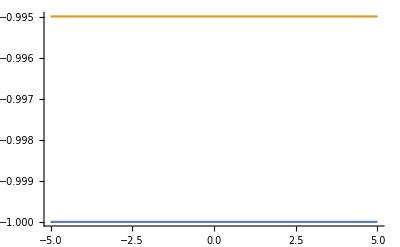

```mathematica
Plot[{-1/2(-1+3 u0d[0.59,y]^2)//Simplify,a3[t,0,x,y]/.a3Rule/.x->0.59},{y,-5,5}]
```

Export a3 Initial data

```mathematica
a3Data=Table[(a3[t,0,x,y]/.a3Rule/.x->xValues[[i]]/.y->yValues[[j]])(*(1+(RandomReal[]-0.5)/100)*),{i,1,xValues//Length},{j,1,yValues//Length}];
```

```mathematica
a3Data[[13,1]]
```

-0.994996

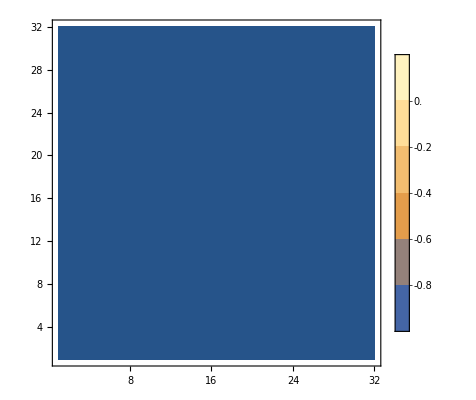

```mathematica
ListContourPlot[a3Data,PlotLegends->Automatic]
```

```mathematica
a3AttributesAndData={"a3"->a3Data};
```

```mathematica
Export["/home/giulio/University/PhD/JeccoNewTest/Jecco_G/examples/Initiala3_BBB.h5",a3AttributesAndData,"Datasets"]
```

/home/giulio/University/PhD/JeccoNewTest/Jecco_G/examples/Initiala3_BBB.h5

```mathematica
Import["/home/giulio/University/PhD/JeccoNewTest/Jecco_G/examples/Initiala3_BBB.h5","Data"]//Keys
```

{/a3}

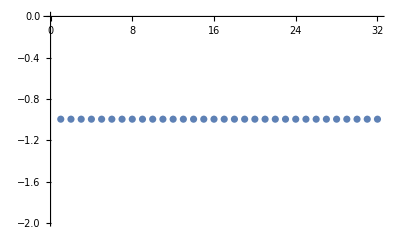

```mathematica
ListPlot[Import["/home/giulio/University/PhD/JeccoNewTest/Jecco_G/examples/Initiala3_BBB.h5","Data"][[1,1]]]
```

#### f1

Same procedure as above but for F1.

```mathematica
FExp=u f1[t,z,y]+Derivative[0,1,0][ξ][t,x,y];
```

```mathematica
FExpOfρ=FExp/.u->rofρ[ρ,x,y]^-1(*/.c1Rule*)(*/.ξ->Function[{t,z,y},0]*)//Series[#,{ρ,0,4}]&;
```

Turbulence draft

```mathematica
(*FToMatch=(b ρ)^3/ρ^2 u0d[x,y] u1d[x,y]*)
```

∂_u Fy=

```mathematica
(*Series[D[rofρ[ρ,x,y],ρ],{ρ,0,3}]*)
```

Chasler paper

```mathematica
FToMatch=-(b ρ(*ofu[{0,x,y}]*))^3/(ρ(*ofu[{0,x,y}]*))^2 u0d[x,y] u1d[x,y];
```

```mathematica
(*Coefficient[FToMatch,ρ]==Coefficient[FExpOfρ,ρ]*)
```

```mathematica
fxRule=Solve[Coefficient[FToMatch,ρ]==Coefficient[FExpOfρ,ρ],f1[t,z,y]]//Simplify
```

{{f1[t,z,y]→0.}}

From Chasler paper this should be.

```mathematica
(*-u0d[x,y] u1d[x,y]*)
```

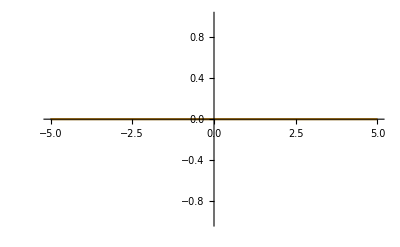

```mathematica
Plot[{-u0d[1.48,y] u1d[1.48,y],fxRule[[1,1,2]]/.x->1.48},{y,yMin,yMax}]
```

```mathematica
DSolve[SeriesCoefficient[FToMatch,{ρ,0,0}]==SeriesCoefficient[FExpOfρ,{ρ,0,0}],ξ,{t,x,y}]//Flatten
```

{ξ→Function[{t,x,y},C[1][t,y]]}

ξ can’t depend on x!

Export fx initial data

```mathematica
fxData=Table[((f1[t,z,y]/.fxRule[[1]])/.x->xValues[[i]]/.y->yValues[[j]])(1+(RandomReal[]-0.5)/100),{i,1,xValues//Length},{j,1,yValues//Length}];
```

```mathematica
(*fxRule*)
```

```mathematica
fxData//Dimensions
```

{32,32}

```mathematica
ListPlot3D[fxData]
```

-Graphics3D-

```mathematica
fxAttributesAndData={"fx"->fxData};
```

```mathematica
Export["/home/giulio/University/PhD/JeccoNewTest/Jecco_G/examples/Initialfx_BBB.h5",fxAttributesAndData,"Datasets"]
```

/home/giulio/University/PhD/JeccoNewTest/Jecco_G/examples/Initialfx_BBB.h5

```mathematica
(*Import["/home/giulio/University/PhD/JeccoNewTest/Jecco_G/examples/Initialfx_BBB.h5","Data"]*)
```

#### f2

Same procedure as above but for F1.

```mathematica
F2Exp=u f2[t,z,y]+Derivative[0,0,1][ξ][t,x,y];
```

```mathematica
F2ExpOfρ=F2Exp/.u->rofρ[ρ,x,y]^-1(*/.c1Rule*)(*/.ξ->Function[{t,z,y},0]*)//Series[#,{ρ,0,4}]&;
```

Turbulence draft

```mathematica
(*FToMatch=(b ρ)^3/ρ^2 u0d[x,y] u1d[x,y]*)
```

∂_u Fy=

```mathematica
(*Series[D[rofρ[ρ,x,y],ρ],{ρ,0,3}]*)
```

Chasler paper

```mathematica
F2ToMatch=-(b ρ(*ofu[{0,x,y}]*))^3/(ρ(*ofu[{0,x,y}]*))^2 u0d[x,y] u2d[x,y];
```

```mathematica
(*Coefficient[FToMatch,ρ]==Coefficient[FExpOfρ,ρ]*)
```

```mathematica
fyRule=Solve[Coefficient[F2ToMatch,ρ]==Coefficient[F2ExpOfρ,ρ],f2[t,z,y]]//Simplify
```

{{f2[t,z,y]→0.}}

From Chasler paper this should be.

```mathematica
(*-u0d[x,y] u1d[x,y]*)
```

```mathematica
Plot[{-u0d[1.48,y] u2d[1.48,y],fyRule[[1,1,2]]/.x->1.48},{y,yMin,yMax}]
```

-Graphics-

```mathematica
DSolve[SeriesCoefficient[F2ToMatch,{ρ,0,0}]==SeriesCoefficient[F2ExpOfρ,{ρ,0,0}],ξ,{t,x,y}]//Flatten
```

{ξ→Function[{t,x,y},C[1][t,x]]}

ξ can’t depend on x!

Export fx initial data

```mathematica
fyData=Table[(f2[t,z,y]/.fyRule[[1]])/.x->xValues[[i]]/.y->yValues[[j]],{i,1,xValues//Length},{j,1,yValues//Length}];
```

```mathematica
(*fxRule*)
```

```mathematica
fyData//Dimensions
```

{32,32}

```mathematica
ListPlot3D[fyData]
```

-Graphics3D-

```mathematica
fyAttributesAndData={"fy"->fyData};
```

```mathematica
Export["/home/giulio/University/PhD/JeccoNewTest/Jecco_G/examples/Initialfy_BBB.h5",fyAttributesAndData,"Datasets"]
```

/home/giulio/University/PhD/JeccoNewTest/Jecco_G/examples/Initialfy_BBB.h5

```mathematica
(*Import["/home/giulio/University/PhD/JeccoNewTest/Jecco_G/examples/Initialfx_BBB.h5","Data"]*)
```

### B Function

#### Grid For ρ

The initial data for B is different, since B is defined through the entire domain. We need to invert the function r(ρ). This is a problem, since that is not invertible analytically.

```mathematica
ClearAll[uofρ]
```

```mathematica
(*uofρ[ρs_,xs_,ys_]:=rofρ[[2]]^-1/.c1Rule[[1]]/.ξ->Function[{t,x,y},0]/.ρ->ρs/.x->xs/.y->ys*)
```

```mathematica
uofρ=Function[{ρs,xs,ys},rofρ[[2]]^-1/.c1Rule[[1]]/.ξ->Function[{t,x,y},0]/.ρ->ρs/.x->xs/.y->ys]
```

Function[{ρs,xs,ys},1/rofρ⟦2⟧/.c1Rule⟦1⟧/.ξ→Function[{t,x,y},0]/.ρ→ρs/.x→xs/.y→ys]

Horizon location

```mathematica
Minimize[uofρ[1,x,y],{x,y(*,xMin,xMax*)}][[1]]//Print
Maximize[uofρ[1,x,y],{x,y(*,xMin,xMax*)}][[1]]//Print
```

1.

1.

```mathematica
Plot3D[uofρ[1,x,y],{x,xMin,xMax},{y,yMin,yMax},PlotLegends->Automatic,(*PlotRange->All,*)(*MaxRecursion->4,*)ColorFunction->"TemperatureMap"]
```

-Graphics3D-

```mathematica
(*uofρToInt=ParallelTable[{MyGrid[[i,j,k]],uofρ[MyGrid[[i,j,k]][[1]],MyGrid[[i,j,k]][[2]],MyGrid[[i,j,k]][[3]]]},{i,1,MyGrid//Length},{j,1,MyGrid[[1]]//Length},{k,1,MyGrid[[1,1]]//Length}];//AbsoluteTiming*)
```

```mathematica
(*ρofuOld2=InverseFunction[Function[{ρ,x,y},Intuofρ[ρ,x,y]],1,3];*)
```

```mathematica
ρofuOld=InverseFunction[Function[{ρ,x,y},uofρ[ρ,x,y]],1,3];
```

```mathematica
ClearAll[ρofu,ρofu2]
```

```mathematica
ρofu=Function[C,ρofuOld[C[[1]],C[[2]],C[[3]]]]
```

Function[C,ρofuOld[C⟦1⟧,C⟦2⟧,C⟦3⟧]]

```mathematica
(*ρofu2=Function[C,ρofuOld2[C[[1]],C[[2]],C[[3]]]]*)
```

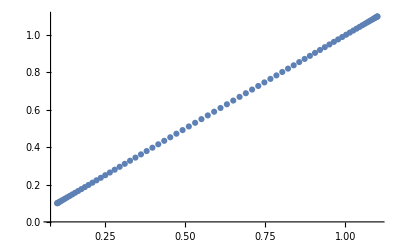

```mathematica
ListPlot[{uValues[[uInnerNodes;;]],Table[ρofu[{uValues[[i]]//N,xMin,yMin}],{i,uInnerNodes,uValues//Length}]}//Transpose(*,{x,-5,5}*),PlotRange->All]
```

```mathematica
(*ListPlot[{uValues[[uInnerNodes;;]],Table[ρofu2[{uValues[[i]],xMin,yMin}],{i,uInnerNodes,uValues//Length}]}//Transpose(*,{x,-5,5}*),PlotRange->All]*)
```

```mathematica
(*ParallelTable[ρofu2[MyGrid[[1,j,k]]](*,{i,1,uValues//Length}*),{j,1,xValues//Length},{k,1,yValues//Length}];//AbsoluteTiming*)
```

```mathematica
MyGrid//Dimensions
```

{103,32,32,3}

```mathematica
ρofuValues=ParallelTable[ρofu[MyGrid[[i,j,k]]],{i,1,uValues//Length},{j,1,xValues//Length},{k,1,yValues//Length}];//AbsoluteTiming
```

{2.88634,Null}

```mathematica
u1Values=Table[u1d[xValues[[i]],yValues[[j]]],{i,1,xValues//Length},{j,1,yValues//Length}];//AbsoluteTiming
```

{0.008693,Null}

```mathematica
u2Values=Table[u2d[xValues[[i]],yValues[[j]]],{i,1,xValues//Length},{j,1,yValues//Length}];//AbsoluteTiming
```

{0.001431,Null}

```mathematica
u0Values=Table[u0d[xValues[[i]],yValues[[j]]],{i,1,xValues//Length},{j,1,yValues//Length}];//AbsoluteTiming
```

{0.411606,Null}

#### B Function

```mathematica
ClearAll[InitialBAnalytic]
```

```mathematica
InitialBAnalytic[u_,x_,y_]:=-1/2 Log[(1+(b ρofu[{u,x,y}])^3 u1d[x,y]^2)/(1+(b ρofu[{u,x,y}])^3 u2d[x,y]^2)] u^-3;
```

```mathematica
InitialB1=ParallelTable[N[SeriesCoefficient[InitialBAnalytic[u,xValues[[i]],yValues[[j]]],{u,uValues[[1]],0}]//Normal](*(1+ (RandomReal[]-0.5)/100)*),{i,1,xNodes},{j,1,yNodes}];//AbsoluteTiming
```

{0.046605,Null}

```mathematica
InitialB=ParallelTable[N[-1/2 Log[(1+(b ρofuValues[[ui,xi,yi]])^3 u1Values[[xi,yi]]^2)/(1+(b ρofuValues[[ui,xi,yi]])^3 u2Values[[xi,yi]]^2)] uValues[[ui]]^-3,$MinPrecision](*(1+(RandomReal[]-0.5)/100)*),{ui,1,uValues//Length},{xi,1,xNodes},{yi,1,yNodes}];//AbsoluteTiming
InitialB[[1]]=InitialB1(*Table[-0.5,{i,1,25},{j,1,25}]*);
(*InitialB[[1]]=InitialB[[2]];*)
```

Power::infy: Infinite expression 1/0^3 encountered.

Infinity::indet: Indeterminate expression 0. ComplexInfinity encountered.

Power::infy: Infinite expression 1/0^3 encountered.

Infinity::indet: Indeterminate expression 0. ComplexInfinity encountered.

Power::infy: Infinite expression 1/0^3 encountered.

General::stop: Further output of Power::infy will be suppressed during this calculation.

Infinity::indet: Indeterminate expression 0. ComplexInfinity encountered.

General::stop: Further output of Infinity::indet will be suppressed during this calculation.

{0.581384,Null}

```mathematica
InitialB//Dimensions
```

{103,32,32}

```mathematica
(*Table[InitialB[[1,i,j]]=-u1d[xValues[[i]],yValues[[j]]]^2/2,{i,1,xValues//Length},{j,1,yValues//Length}];*)
```

```mathematica
(*ListContourPlot[InitialB[[1]],PlotLegends->Automatic]*)
```

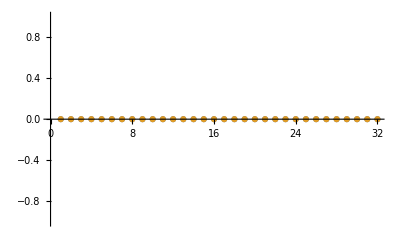

```mathematica
ListPlot[{InitialB[[1,1,;;]],Table[-u1d[xValues[[1]],yValues[[i]]]^2/2(*-InitialB[[1,1,i]]*),{i,1,yValues//Length}]}(*,Joined->True*)(*,PlotStyle->{Dashed,Dotted}*)]
```

```mathematica
(*phiFunc=InterpolatingFunction[…]*)
```

```mathematica
(*phi=Table[phiFunc[uValues[[i]]],{i,1,uValues//Length},{j,1,xValues//Length},{k,1,yValues//Length}];*)
```

```mathematica
ExportData=Join[{InitialB(*phi*)[[;;uInnerNodes,;;,;;]]},Table[InitialB(*phi*)[[ uInnerNodes+(uOuterNodes-1) i;;uInnerNodes+(uOuterNodes-1) (i+1),;;,;;]],{i,0,uOuterDomains-1}]];//AbsoluteTiming
```

{0.000231,Null}

```mathematica
ExportAttributes=Table[ToString[i],{i,1,uOuterDomains+1}];
```

```mathematica
AttributesAndData=Table[ExportAttributes[[i]]->ExportData[[i]],{i,1,ExportAttributes//Length}];//AbsoluteTiming
```

{0.000644,Null}

```mathematica
Export["/home/giulio/University/PhD/JeccoNewTest/Jecco_G/examples/InitialB_BBB.h5",AttributesAndData,"Datasets"]
```

/home/giulio/University/PhD/JeccoNewTest/Jecco_G/examples/InitialB_BBB.h5

#### B2 Function

```mathematica
Maxg=FindMaxValue[{Abs[InterpolatingFunction[…][z]//Re],0<=z<=1},z];
```

$MinPrecision::preccon: Cannot set $MinPrecision such that $MaxPrecision < $MinPrecision.

InterpolatingFunction::dmval: Input value {-0.0000320803} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {-0.0000260249} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {-0.000113482} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

```mathematica
Maxg
```

15.7958

ExpOfHxy=Exp[-ⅈ ω (t- Integrate[1/f[z],z])]

```mathematica
ExpOfHxy[tt_,u_]:=E^(-ⅈ ω (tt-ArcTan[u]/2+1/4 Log[1-u]-1/4 Log[1+u]))/.ω->6.7695647406369571731714695802563491731559856549638116837474665910478434107167`55. ⅈ
```

```mathematica
Parametricgxy[u_]:=1/20 ExpOfHxy[0,u]InterpolatingFunction[…][u]/Maxg//Re;
```

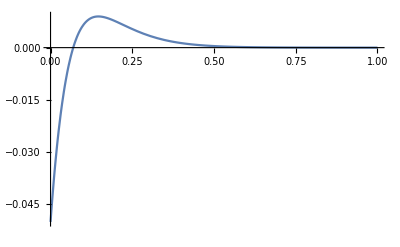

```mathematica
Plot[Parametricgxy[u],{u,0,1},PlotRange->All]
```

```mathematica
Series[-Log[(1-4 a^2 u^8)^(1/6)]/u^4,{u,0,4}]
```

(2 a^2 u^4)/3+O[u]^5

```mathematica
Solve[{S^2 E^(-u^4 B1in-u^4 B2in)Cosh[u^4 Gin]==u^-2,S^2 E^(u^4 B1in-u^4 B2in)Cosh[u^4 Gin]==u^-2,S^2 E^(-u^4 B2in)Sinh[u^4 Gin]==2 u^2 a,S^2 E^(2 u^4 B2in)==u^-2},{S,Gin,B1in,B2in}]/. C[1]->0/. C[2]->0/.C[3]->0
```

{{S→-((1-4 a^2 u^8)^(1/6))/u,Gin→Log[(-√(1-4 a^2 u^8)-2 a u^4 √(1-4 a^2 u^8))/(-1+4 a^2 u^8)]/u^4,B1in→0,B2in→-Log[(1-4 a^2 u^8)^(1/6)]/u^4},{S→-((1-4 a^2 u^8)^(1/6))/u,Gin→Log[(√(1-4 a^2 u^8)-2 a u^4 √(1-4 a^2 u^8))/(-1+4 a^2 u^8)]/u^4,B1in→-(ⅈ π)/u^4,B2in→-Log[(1-4 a^2 u^8)^(1/6)]/u^4},{S→-((1-4 a^2 u^8)^(1/6))/u,Gin→Log[(-√(1-4 a^2 u^8)+2 a u^4 √(1-4 a^2 u^8))/(-1+4 a^2 u^8)]/u^4,B1in→-(ⅈ π)/u^4,B2in→-Log[-(1-4 a^2 u^8)^(1/6)]/u^4},{S→-((1-4 a^2 u^8)^(1/6))/u,Gin→Log[(√(1-4 a^2 u^8)+2 a u^4 √(1-4 a^2 u^8))/(-1+4 a^2 u^8)]/u^4,B1in→0,B2in→-Log[-(1-4 a^2 u^8)^(1/6)]/u^4},{S→((1-4 a^2 u^8)^(1/6))/u,Gin→Log[(-√(1-4 a^2 u^8)-2 a u^4 √(1-4 a^2 u^8))/(-1+4 a^2 u^8)]/u^4,B1in→0,B2in→-Log[(1-4 a^2 u^8)^(1/6)]/u^4},{S→((1-4 a^2 u^8)^(1/6))/u,Gin→Log[(√(1-4 a^2 u^8)-2 a u^4 √(1-4 a^2 u^8))/(-1+4 a^2 u^8)]/u^4,B1in→-(ⅈ π)/u^4,B2in→-Log[(1-4 a^2 u^8)^(1/6)]/u^4},{S→((1-4 a^2 u^8)^(1/6))/u,Gin→Log[(-√(1-4 a^2 u^8)+2 a u^4 √(1-4 a^2 u^8))/(-1+4 a^2 u^8)]/u^4,B1in→-(ⅈ π)/u^4,B2in→-Log[-(1-4 a^2 u^8)^(1/6)]/u^4},{S→((1-4 a^2 u^8)^(1/6))/u,Gin→Log[(√(1-4 a^2 u^8)+2 a u^4 √(1-4 a^2 u^8))/(-1+4 a^2 u^8)]/u^4,B1in→0,B2in→-Log[-(1-4 a^2 u^8)^(1/6)]/u^4},{S→-((-1)^(1/3) (1-4 a^2 u^8)^(1/6))/u,Gin→Log[(-√(1-4 a^2 u^8)-2 a u^4 √(1-4 a^2 u^8))/(-1+4 a^2 u^8)]/u^4,B1in→0,B2in→-Log[-(-1)^(1/3) (1-4 a^2 u^8)^(1/6)]/u^4},{S→-((-1)^(1/3) (1-4 a^2 u^8)^(1/6))/u,Gin→Log[(√(1-4 a^2 u^8)-2 a u^4 √(1-4 a^2 u^8))/(-1+4 a^2 u^8)]/u^4,B1in→-(ⅈ π)/u^4,B2in→-Log[-(-1)^(1/3) (1-4 a^2 u^8)^(1/6)]/u^4},{S→-((-1)^(1/3) (1-4 a^2 u^8)^(1/6))/u,Gin→Log[(-√(1-4 a^2 u^8)+2 a u^4 √(1-4 a^2 u^8))/(-1+4 a^2 u^8)]/u^4,B1in→-(ⅈ π)/u^4,B2in→-Log[(-1)^(1/3) (1-4 a^2 u^8)^(1/6)]/u^4},{S→-((-1)^(1/3) (1-4 a^2 u^8)^(1/6))/u,Gin→Log[(√(1-4 a^2 u^8)+2 a u^4 √(1-4 a^2 u^8))/(-1+4 a^2 u^8)]/u^4,B1in→0,B2in→-Log[(-1)^(1/3) (1-4 a^2 u^8)^(1/6)]/u^4},{S→((-1)^(1/3) (1-4 a^2 u^8)^(1/6))/u,Gin→Log[(-√(1-4 a^2 u^8)-2 a u^4 √(1-4 a^2 u^8))/(-1+4 a^2 u^8)]/u^4,B1in→0,B2in→-Log[-(-1)^(1/3) (1-4 a^2 u^8)^(1/6)]/u^4},{S→((-1)^(1/3) (1-4 a^2 u^8)^(1/6))/u,Gin→Log[(√(1-4 a^2 u^8)-2 a u^4 √(1-4 a^2 u^8))/(-1+4 a^2 u^8)]/u^4,B1in→-(ⅈ π)/u^4,B2in→-Log[-(-1)^(1/3) (1-4 a^2 u^8)^(1/6)]/u^4},{S→((-1)^(1/3) (1-4 a^2 u^8)^(1/6))/u,Gin→Log[(-√(1-4 a^2 u^8)+2 a u^4 √(1-4 a^2 u^8))/(-1+4 a^2 u^8)]/u^4,B1in→-(ⅈ π)/u^4,B2in→-Log[(-1)^(1/3) (1-4 a^2 u^8)^(1/6)]/u^4},{S→((-1)^(1/3) (1-4 a^2 u^8)^(1/6))/u,Gin→Log[(√(1-4 a^2 u^8)+2 a u^4 √(1-4 a^2 u^8))/(-1+4 a^2 u^8)]/u^4,B1in→0,B2in→-Log[(-1)^(1/3) (1-4 a^2 u^8)^(1/6)]/u^4},{S→-((-1)^(2/3) (1-4 a^2 u^8)^(1/6))/u,Gin→Log[(-√(1-4 a^2 u^8)-2 a u^4 √(1-4 a^2 u^8))/(-1+4 a^2 u^8)]/u^4,B1in→0,B2in→-Log[(-1)^(2/3) (1-4 a^2 u^8)^(1/6)]/u^4},{S→-((-1)^(2/3) (1-4 a^2 u^8)^(1/6))/u,Gin→Log[(√(1-4 a^2 u^8)-2 a u^4 √(1-4 a^2 u^8))/(-1+4 a^2 u^8)]/u^4,B1in→-(ⅈ π)/u^4,B2in→-Log[(-1)^(2/3) (1-4 a^2 u^8)^(1/6)]/u^4},{S→-((-1)^(2/3) (1-4 a^2 u^8)^(1/6))/u,Gin→Log[(-√(1-4 a^2 u^8)+2 a u^4 √(1-4 a^2 u^8))/(-1+4 a^2 u^8)]/u^4,B1in→-(ⅈ π)/u^4,B2in→-Log[-(-1)^(2/3) (1-4 a^2 u^8)^(1/6)]/u^4},{S→-((-1)^(2/3) (1-4 a^2 u^8)^(1/6))/u,Gin→Log[(√(1-4 a^2 u^8)+2 a u^4 √(1-4 a^2 u^8))/(-1+4 a^2 u^8)]/u^4,B1in→0,B2in→-Log[-(-1)^(2/3) (1-4 a^2 u^8)^(1/6)]/u^4},{S→((-1)^(2/3) (1-4 a^2 u^8)^(1/6))/u,Gin→Log[(-√(1-4 a^2 u^8)-2 a u^4 √(1-4 a^2 u^8))/(-1+4 a^2 u^8)]/u^4,B1in→0,B2in→-Log[(-1)^(2/3) (1-4 a^2 u^8)^(1/6)]/u^4},{S→((-1)^(2/3) (1-4 a^2 u^8)^(1/6))/u,Gin→Log[(√(1-4 a^2 u^8)-2 a u^4 √(1-4 a^2 u^8))/(-1+4 a^2 u^8)]/u^4,B1in→-(ⅈ π)/u^4,B2in→-Log[(-1)^(2/3) (1-4 a^2 u^8)^(1/6)]/u^4},{S→((-1)^(2/3) (1-4 a^2 u^8)^(1/6))/u,Gin→Log[(-√(1-4 a^2 u^8)+2 a u^4 √(1-4 a^2 u^8))/(-1+4 a^2 u^8)]/u^4,B1in→-(ⅈ π)/u^4,B2in→-Log[-(-1)^(2/3) (1-4 a^2 u^8)^(1/6)]/u^4},{S→((-1)^(2/3) (1-4 a^2 u^8)^(1/6))/u,Gin→Log[(√(1-4 a^2 u^8)+2 a u^4 √(1-4 a^2 u^8))/(-1+4 a^2 u^8)]/u^4,B1in→0,B2in→-Log[-(-1)^(2/3) (1-4 a^2 u^8)^(1/6)]/u^4}}

```mathematica
InitialB2=ParallelTable[N[-Log[(1-4 a^2 u^8)^(1/6)]/u^4/.a->Parametricgxy[uValues[[ui]]]/.u->uValues[[ui]],$MinPrecision],{ui,1,uValues//Length},{xi,1,xNodes},{yi,1,yNodes}];//AbsoluteTiming
```

InterpolatingFunction::dmval: Input value {1.024491681045681953601531004276832149691709130880192856967105393} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

InterpolatingFunction::dmval: Input value {1.052920196832761605015795291404792005793337833604905915370574892} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {1.07491006586389132885131328238047473284403663414797247068004738} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

InterpolatingFunction::dmval: Input value {1.07491006586389132885131328238047473284403663414797247068004738} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

InterpolatingFunction::dmval: Input value {1.090148683402318070379897764154224147285293185095574613420011428} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

InterpolatingFunction::dmval: Input value {1.098419419507347924414986400827153106268867738622415312382752078} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

InterpolatingFunction::dmval: Input value {1.002158282635382400086941442423348516223148347131070448252196111} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

{185.4,Null}

```mathematica
InitialB2uzero=ParallelTable[0,{i,1,xNodes},{j,1,yNodes}];//AbsoluteTiming
```

{0.012855,Null}

{0.018013,Null}

{0.014223,Null}

{0.0163,Null}

```mathematica
InitialB2[[1]]=InitialB2uzero;
```

```mathematica
ExportDataB2=Join[{InitialB2(*phi*)[[;;uInnerNodes,;;,;;]]},Table[InitialB2(*phi*)[[ uInnerNodes+(uOuterNodes-1) i;;uInnerNodes+(uOuterNodes-1) (i+1),;;,;;]],{i,0,uOuterDomains-1}]];//AbsoluteTiming
```

{0.00021,Null}

```mathematica
ExportAttributesB2=Table[ToString[i],{i,1,uOuterDomains+1}];
```

```mathematica
AttributesAndDataB2=Table[ExportAttributesB2[[i]]->ExportDataB2[[i]],{i,1,ExportAttributesB2//Length}];//AbsoluteTiming
```

{0.003879,Null}

```mathematica
Export["/home/giulio/University/PhD/JeccoNewTest/Jecco_G/examples/InitialB2_BBB.h5",AttributesAndDataB2,"Datasets"]
```

/home/giulio/University/PhD/JeccoNewTest/Jecco_G/examples/InitialB2_BBB.h5

#### G Function

```mathematica
Maxg=FindMaxValue[{Abs[InterpolatingFunction[…][z]//Re],0<=z<=1},z];
```

$MinPrecision::preccon: Cannot set $MinPrecision such that $MaxPrecision < $MinPrecision.

InterpolatingFunction::dmval: Input value {-0.0000320803} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {-0.0000260249} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {-0.000113482} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

```mathematica
ExpOfHxy[tt_,u_]:=E^(-ⅈ ω (tt-ArcTan[u]/2+1/4 Log[1-u]-1/4 Log[1+u]))/.ω->6.7695647406369571731714695802563491731559856549638116837474665910478434107167`55. ⅈ
```

```mathematica
Parametricgxy[u_]:=1/20 ExpOfHxy[0,u]InterpolatingFunction[…][u]/Maxg//Re;
```

```mathematica
Plot[Parametricgxy[u],{u,0,1},PlotRange->All]
```

-Graphics-

```mathematica
Series[Log[(-√(1-4 a^2 u^8)-2 a u^4 √(1-4 a^2 u^8))/(-1+4 a^2 u^8)]/u^4,{u,0,4}]
```

2 a+O[u]^5

```mathematica
Solve[{S^2 E^(-u^4 B1in-u^4 B2in)Cosh[u^4 Gin]==u^-2,S^2 E^(u^4 B1in-u^4 B2in)Cosh[u^4 Gin]==u^-2,S^2 E^(-u^4 B2in)Sinh[u^4 Gin]==2 u^2 a,S^2 E^(2 u^4 B2in)==u^-2},{S,Gin,B1in,B2in}][[1]]/. C[1]->0/. C[2]->0/.C[3]->0
```

{S→-((1-4 a^2 u^8)^(1/6))/u,Gin→Log[(-√(1-4 a^2 u^8)-2 a u^4 √(1-4 a^2 u^8))/(-1+4 a^2 u^8)]/u^4,B1in→0,B2in→-Log[(1-4 a^2 u^8)^(1/6)]/u^4}

```mathematica
InitialG=ParallelTable[N[Log[(-√(1-4 a^2 u^8)-2 a u^4 √(1-4 a^2 u^8))/(-1+4 a^2 u^8)]/u^4/.a->Parametricgxy[uValues[[ui]]]/.u->uValues[[ui]],$MinPrecision],{ui,1,uValues//Length},{xi,1,xNodes},{yi,1,yNodes}];//AbsoluteTiming
```

InterpolatingFunction::dmval: Input value {1.024491681045681953601531004276832149691709130880192856967105393} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

InterpolatingFunction::dmval: Input value {1.052920196832761605015795291404792005793337833604905915370574892} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

InterpolatingFunction::dmval: Input value {1.07491006586389132885131328238047473284403663414797247068004738} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

InterpolatingFunction::dmval: Input value {1.090148683402318070379897764154224147285293185095574613420011428} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

InterpolatingFunction::dmval: Input value {1.098419419507347924414986400827153106268867738622415312382752078} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

InterpolatingFunction::dmval: Input value {1.002158282635382400086941442423348516223148347131070448252196111} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

{244.647,Null}

```mathematica
InitialG1=ParallelTable[2a/.a->Parametricgxy[uValues[[1]]],{i,1,xNodes},{j,1,yNodes}];//AbsoluteTiming
```

{3.09356,Null}

```mathematica
InitialG[[1]]=InitialG1;
```

```mathematica
ExportDataG=Join[{InitialG(*phi*)[[;;uInnerNodes,;;,;;]]},Table[InitialG(*phi*)[[ uInnerNodes+(uOuterNodes-1) i;;uInnerNodes+(uOuterNodes-1) (i+1),;;,;;]],{i,0,uOuterDomains-1}]];//AbsoluteTiming
```

{0.000204,Null}

```mathematica
ExportAttributesG=Table[ToString[i],{i,1,uOuterDomains+1}];
```

```mathematica
AttributesAndDataG=Table[ExportAttributesG[[i]]->ExportDataG[[i]],{i,1,ExportAttributesG//Length}];//AbsoluteTiming
```

{0.002301,Null}

```mathematica
Export["/home/giulio/University/PhD/JeccoNewTest/Jecco_G/examples/InitialG_BBB.h5",AttributesAndDataG,"Datasets"]
```

/home/giulio/University/PhD/JeccoNewTest/Jecco_G/examples/InitialG_BBB.h5

/home/giulio/University/PhD/JeccoNewTest/Jecco_G/examples/InitialG_BBB.h5

#### ϕ Function

```mathematica
(*Export["/home/giulio/University/PhD/JeccoNewTest/Jecco_G/examples/Initialphi_BB.h5",AttributesAndData,"Datasets"]*)
```

```mathematica
testImport=Import["/home/giulio/University/PhD/JeccoNewTest/Jecco_G/examples/InitialB_BBB.h5","Data"]
```

## BM

```mathematica
Solve[{S^2 E^-B1 Cosh[G]==u^-2,S^2 E^B1 Cosh[G]==u^-2,S^2 2 Sinh[G]==a},{S,G,B1}]/. C[1]->0/. C[2]->0
```

{{S→-((4-a^2 u^4)^(1/4))/(√2 u),G→Log[(-2 √(4-a^2 u^4)-a u^2 √(4-a^2 u^4))/(-4+a^2 u^4)],B1→0},{S→-((4-a^2 u^4)^(1/4))/(√2 u),G→Log[(2 √(4-a^2 u^4)-a u^2 √(4-a^2 u^4))/(-4+a^2 u^4)],B1→-ⅈ π},{S→-(ⅈ (4-a^2 u^4)^(1/4))/(√2 u),G→Log[(-2 √(4-a^2 u^4)+a u^2 √(4-a^2 u^4))/(-4+a^2 u^4)],B1→-ⅈ π},{S→-(ⅈ (4-a^2 u^4)^(1/4))/(√2 u),G→Log[(2 √(4-a^2 u^4)+a u^2 √(4-a^2 u^4))/(-4+a^2 u^4)],B1→0},{S→(ⅈ (4-a^2 u^4)^(1/4))/(√2 u),G→Log[(-2 √(4-a^2 u^4)+a u^2 √(4-a^2 u^4))/(-4+a^2 u^4)],B1→-ⅈ π},{S→(ⅈ (4-a^2 u^4)^(1/4))/(√2 u),G→Log[(2 √(4-a^2 u^4)+a u^2 √(4-a^2 u^4))/(-4+a^2 u^4)],B1→0},{S→((4-a^2 u^4)^(1/4))/(√2 u),G→Log[(-2 √(4-a^2 u^4)-a u^2 √(4-a^2 u^4))/(-4+a^2 u^4)],B1→0},{S→((4-a^2 u^4)^(1/4))/(√2 u),G→Log[(2 √(4-a^2 u^4)-a u^2 √(4-a^2 u^4))/(-4+a^2 u^4)],B1→-ⅈ π}}

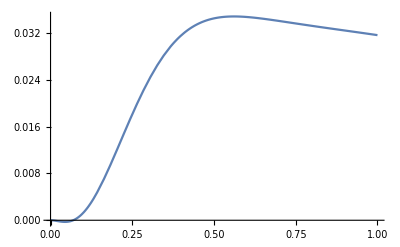

```mathematica
Plot[Log[(-2 √(4-a^2 u^4)-a u^2 √(4-a^2 u^4))/(-4+a^2 u^4)]/.a->Parametricgxy[u],{u,0,1}]
```

```mathematica
((4-a^2 u^4)^(1/4))/(√2 u)/.a->1/10 Parametricgxy[u]/.u->1.1
```

InterpolatingFunction::dmval: Input value {1.1} lies outside the range of data in the interpolating function. Extrapolation will be used.

0.909089

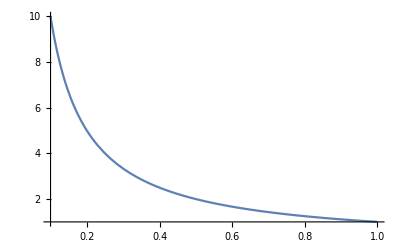

```mathematica
Plot[(*u^-2*)((4-a^2 u^4)^(1/4))/(√2 u)/.a->Parametricgxy[u],{u,0.1,1},PlotRange->All]
```